```mathematica
c = 299792458; (*m/s, Speed of Light in Vacuum*)
ℏ = 1.054571628*10^-34; (*J/s, Planck's constant*)
ϵ0 = 8.854187817*10^-12; (*F/m, Permittivity of Free Space*)
a0 = .529177*10^-10; (* Bohr radius, m *)
kB = 1.38*10^-23;

el = 1.602*10^-19;
AMU=1.66*10^-27*kg;
cm=10^-2;mm=10^-3;μm=10^-6;nm = 10^-9;pm=10^-12;fm=10^-15;
kg=1;g=10^-3;ng=10^-9*g;pg=10^-12*g;
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9; THz = 10^12;
kK=1;mK=10^-3;μK=10^-6;nK=10^-9;
Ww=1;mW=10^-3;μW=10^-6;nW=10^-9;
Pa=1;GPa=10^9;
ms=10^-3;
ohm=1;V=1;mV=10^-3;
ns = 10^-9;

λ689 = 689*10^-9; (*m, in vacuum*)
λ698 = 698*10^-9; (*m, in vacuum*)
λ707 = 707*10^-9; (* m, in vacuum *)
λ813 = 813.4*10^-9; (*m, in vacuum*)
γ3p1 = 2π(7.5*10^3); (*rad/s, atom linewidth FWHM*)
γ3p0 = 2π(.001); (*rad/s, atom linewidth FWHM*)
γ461 = 32*10^6*2π;(*rad/s, atom linewidth FWHM*)
γ707  = 10*10^6*2π; (*NOT ACTUAL, USE FOR NOW*)
Isat461 = 42*10^-3*10^4; (* W/m^2*)
m = 87*1.66*10^-27; (* Sr 87, kg *)
α = 282*4π ϵ0 a0^3; (* dipole polarizability of ground, 3p0 at 813nm, from Boyd thesis *)
ωr = 4.7*1000*2π; (* recoil frequency clock trans ??? *)
```

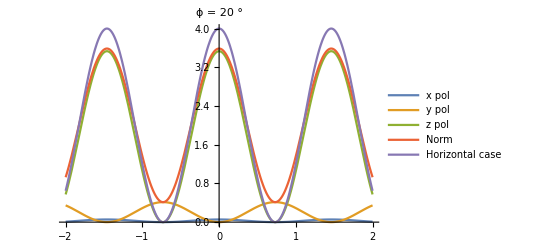

```mathematica
k=2π; 
θ = 20Degree;
ϕ = 20 Degree;

E1 = {Sin[ϕ]Sin[θ],Sin[ϕ]Cos[θ],Cos[ϕ]}*Exp[-I k (x Cos[θ]-y Sin[θ])];
E2 = {Sin[ϕ]Sin[θ],-Sin[ϕ]Cos[θ],Cos[ϕ]}*Exp[-I k (x Cos[θ]+y Sin[θ])];

E1z = Exp[-I k (x Cos[θ]-y Sin[θ])];
E2z =Exp[-I k (x Cos[θ]+y Sin[θ])];

Plot[{Abs[(E1+E2).{1,0,0}]^2/.x->0,Abs[(E1+E2).{0,1,0}]^2/.x->0,Abs[(E1+E2).{0,0,1}]^2/.x->0,Norm[(E1+E2)]^2/.x->0,Abs[(E1z+E2z)]^2/.x->0},{y,-2,2},PlotLegends->{"x pol", "y pol", "z pol","Norm","Horizontal case"},PlotLabel->Row[{"ϕ = ",ϕ}]]
```

```mathematica
Abs[(E1+E2).{1,0,0}]^2/Abs[(E1+E2).{0,0,1}]^2/.{x->0,y-> 0}//N
```

0.0154966

```mathematica
Re[E1+E2]/.{x->0,y->0}//Normalize//N
```

{1.,0.,0.}

```mathematica
4.5*300/1800
```

0.75

```mathematica
4.5*300/1800*(1/2+1/(.75))^-1
```

```mathematica
(2+1/(.75))
```

3.33333